```mathematica
(*Quit[];*)
```

```mathematica
Needs["MaTeX`"]
```

Define spin and orbital angular momentum matrices.

```mathematica
Subscript[l, 1]=({{0, 0, 0}, {0, 0, -I}, {0, I, 0}});
Subscript[l, 2]=({{0, 0, I}, {0, 0, 0}, {-I, 0, 0}});
Subscript[l, 3]=({{0, -I, 0}, {I, 0, 0}, {0, 0, 0}});
Subscript[σ, 0]=IdentityMatrix[2];
Subscript[σ, 1]={{0,1},{1,0}};
Subscript[σ, 2]={{0,-I},{I,0}};
Subscript[σ, 3]={{1,0},{0,-1}};
Id3=IdentityMatrix[3];
Id2=IdentityMatrix[2];
Id6=IdentityMatrix[6];
```

```mathematica
Subscript[S, 1]=1/2 KroneckerProduct[Subscript[σ, 1],Id3];
Subscript[S, 2]=1/2 KroneckerProduct[Subscript[σ, 2],Id3];
Subscript[S, 3]=1/2 KroneckerProduct[Subscript[σ, 3],Id3];
Subscript[L, 1]=KroneckerProduct[Id2,Subscript[l, 1]];
Subscript[L, 2]=KroneckerProduct[Id2,Subscript[l, 2]];
Subscript[L, 3]=KroneckerProduct[Id2,Subscript[l, 3]];
```

Find  eigenstates of the atomic Hamiltonian with spin-orbit coupling and trigonal distortion.

```mathematica
n={1,1,1}/√3;
Ln=Sum[Subscript[L, a] n[[a]],{a,1,3}];
Δ=.1;
ClearAll[Δ];
Hso=Sum[ Subscript[L, a].Subscript[S, a],{a,1,3}]+Δ Ln.Ln
```

{{(2 Δ)/3,-ⅈ/2-Δ/3,-Δ/3,0,0,1/2},{ⅈ/2-Δ/3,(2 Δ)/3,-Δ/3,0,0,-ⅈ/2},{-Δ/3,-Δ/3,(2 Δ)/3,-1/2,ⅈ/2,0},{0,0,-1/2,(2 Δ)/3,ⅈ/2-Δ/3,-Δ/3},{0,0,-ⅈ/2,-ⅈ/2-Δ/3,(2 Δ)/3,-Δ/3},{1/2,ⅈ/2,0,-Δ/3,-Δ/3,(2 Δ)/3}}

```mathematica
Eigenvalues[Hso]
```

{1/2 (1+2 Δ),1/2 (1+2 Δ),1/4 (-1+2 Δ-√(9-4 Δ+4 Δ^2)),1/4 (-1+2 Δ-√(9-4 Δ+4 Δ^2)),1/4 (-1+2 Δ+√(9-4 Δ+4 Δ^2)),1/4 (-1+2 Δ+√(9-4 Δ+4 Δ^2))}

```mathematica
FullSimplify/@{1/2 (1+2 Δ),1/2 (1+2 Δ),1/4 (-1+2 Δ-√(9-4 Δ+4 Δ^2)),1/4 (-1+2 Δ-√(9-4 Δ+4 Δ^2)),1/4 (-1+2 Δ+√(9-4 Δ+4 Δ^2)),1/4 (-1+2 Δ+√(9-4 Δ+4 Δ^2))}
```

{1/2+Δ,1/2+Δ,1/4 (-1+2 Δ-√(9+4 (-1+Δ) Δ)),1/4 (-1+2 Δ-√(9+4 (-1+Δ) Δ)),1/4 (-1+2 Δ+√(9+4 (-1+Δ) Δ)),1/4 (-1+2 Δ+√(9+4 (-1+Δ) Δ))}

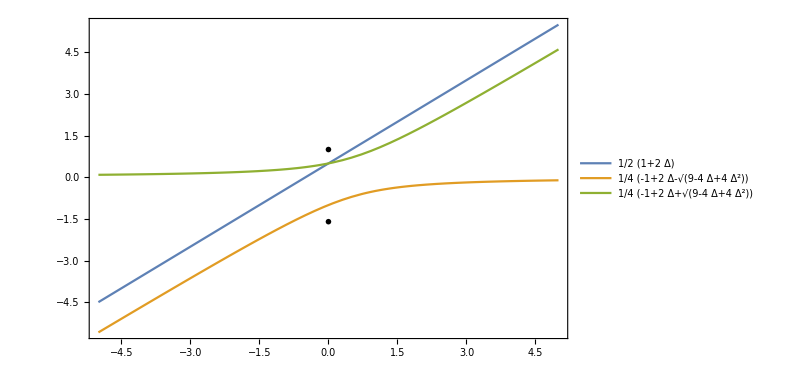

```mathematica
Plot[  {1/2 (1+2 Δ),1/4 (-1+2 Δ-√(9-4 Δ+4 Δ^2)),1/4 (-1+2 Δ+√(9-4 Δ+4 Δ^2))}, {Δ,-5,5},PlotLegends-> Placed[ "Expressions",Scaled[{0.2,0.85}]  ]  ,  FrameLabel->{MaTeX["\\Delta/\\lambda \\quad (\\lambda=1)",Magnification->2] , MaTeX["\\text{Eigenvalues } H_{\\text{tri}}(\\Delta) + H_{\\text{SO}}(\\lambda)",Magnification->1.75] } , Frame->True,  FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,
 Epilog->{Inset[MaTeX["j_{\\text{eff}}=3/2\\; \\downarrow ",Magnification->1.2],{0,1},Scaled[{.94,.5}] ],
Inset[MaTeX["\\uparrow \\; j_{\\text{eff}}=1/2 ",Magnification->1.2],{0,-1.6},Scaled[{.06,.5}] ]                     } 
]
```

```mathematica
MatrixForm/@Transpose[  Transpose[ Eigensystem[Hso] ][[3;;4]]  ]
```

{(1/4 (-1+2 Δ-√(9-4 Δ+4 Δ^2))
1/4 (-1+2 Δ-√(9-4 Δ+4 Δ^2))),(-(9+(2-2 ⅈ) Δ-4 ⅈ Δ^2+3 √(9-4 Δ+4 Δ^2)-2 ⅈ Δ √(9-4 Δ+4 Δ^2))/(9+(2-4 ⅈ) Δ+3 √(9-4 Δ+4 Δ^2)) | (ⅈ (9-4 Δ+4 Δ^2+3 √(9-4 Δ+4 Δ^2)+2 Δ √(9-4 Δ+4 Δ^2)))/(9+(2-4 ⅈ) Δ+3 √(9-4 Δ+4 Δ^2)) | -(2 Δ ((1+2 ⅈ)+2 Δ+√(9-4 Δ+4 Δ^2)))/(9 ⅈ+(4+2 ⅈ) Δ+3 ⅈ √(9-4 Δ+4 Δ^2)) | -((4-4 ⅈ) Δ)/(9 ⅈ+(4+2 ⅈ) Δ+3 ⅈ √(9-4 Δ+4 Δ^2)) | 0 | 1
(2 ((1+2 ⅈ) Δ+2 Δ^2+Δ √(9-4 Δ+4 Δ^2)))/(9 ⅈ+(4+2 ⅈ) Δ+3 ⅈ √(9-4 Δ+4 Δ^2)) | (2 Δ ((1-2 ⅈ)+2 Δ+√(9-4 Δ+4 Δ^2)))/(9 ⅈ+(4+2 ⅈ) Δ+3 ⅈ √(9-4 Δ+4 Δ^2)) | -(ⅈ (9-4 Δ+4 Δ^2+3 √(9-4 Δ+4 Δ^2)+2 Δ √(9-4 Δ+4 Δ^2)))/(9+(2-4 ⅈ) Δ+3 √(9-4 Δ+4 Δ^2)) | -(ⅈ (9+(2+4 ⅈ) Δ+3 √(9-4 Δ+4 Δ^2)))/(9+(2-4 ⅈ) Δ+3 √(9-4 Δ+4 Δ^2)) | 1 | 0)}

```mathematica
FullSimplify[  Transpose[  Transpose[ Eigensystem[Hso] ][[3;;4]]  ][[2]]  , Assumptions-> (Δ>0 &&Δ<1)]
```

{{(-3 (3+√(9+4 (-1+Δ) Δ))+2 ⅈ Δ ((1+ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/(9+(2-4 ⅈ) Δ+3 √(9+4 (-1+Δ) Δ)),(-9+(3-6 ⅈ) √(9+4 (-1+Δ) Δ)-2 Δ (-2+2 Δ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),-(2 Δ ((1+2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),((4+4 ⅈ) Δ)/(9+(2-4 ⅈ) Δ+3 √(9+4 (-1+Δ) Δ)),0,1},{(2 Δ ((1+2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),(2 Δ ((1-2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),(9-(3-6 ⅈ) √(9+4 (-1+Δ) Δ)+2 Δ (-2+2 Δ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),((2-2 ⅈ) Δ+(3+3 ⅈ) (3 ⅈ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),1,0}}

```mathematica
v1={(-3 (3+√(9+4 (-1+Δ) Δ))+2 ⅈ Δ ((1+ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/(9+(2-4 ⅈ) Δ+3 √(9+4 (-1+Δ) Δ)),(-9+(3-6 ⅈ) √(9+4 (-1+Δ) Δ)-2 Δ (-2+2 Δ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),-(2 Δ ((1+2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),((4+4 ⅈ) Δ)/(9+(2-4 ⅈ) Δ+3 √(9+4 (-1+Δ) Δ)),0,1}
v2={(2 Δ ((1+2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),(2 Δ ((1-2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),(9-(3-6 ⅈ) √(9+4 (-1+Δ) Δ)+2 Δ (-2+2 Δ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),((2-2 ⅈ) Δ+(3+3 ⅈ) (3 ⅈ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),1,0}
```

```mathematica
Sort[Eigensystem[N[Hso]]]
```

{{-0.934847,-0.934847,0.6,0.6,0.534847,0.534847},{{0.576347-0.0125713 ⅈ,0.0129163-0.576226 ⅈ,0.000298515+0.00477166 ⅈ,-0.0262932+0.0175677 ⅈ,-0.0312432-0.012393 ⅈ,-0.57733+0. ⅈ},{0.0158918-0.0273388 ⅈ,-0.0143196-0.0304084 ⅈ,-0.0360473-0.576204 ⅈ,-0.0234391-0.576007 ⅈ,0.574296-0.0488694 ⅈ,-0.00478099+0. ⅈ},{-0.353635-0.29941 ⅈ,0.29941-0.269145 ⅈ,0.0542248+0.568555 ⅈ,-0.269145-0.21492 ⅈ,0.353635+0.21492 ⅈ,-0.0844896+0. ⅈ},{0.239503+0.247524 ⅈ,-0.247524-0.331632 ⅈ,0.00802163+0.0841079 ⅈ,-0.331632-0.323611 ⅈ,-0.239503+0.323611 ⅈ,0.571135+0. ⅈ},{-0.387473+0.366444 ⅈ,-0.326417-0.186847 ⅈ,-0.524521-0.0637472 ⅈ,0.12249+0.184155 ⅈ,0.136438+0.416243 ⅈ,-0.232697+0. ⅈ},{-0.143813+0.168032 ⅈ,-0.18566+0.396742 ⅈ,0.230997+0.0280741 ⅈ,-0.340433-0.410514 ⅈ,-0.346575+0.146101 ⅈ,-0.52838+0. ⅈ}}}

```mathematica
Ln.Ln//MatrixForm
```

(2/3 | -1/3 | -1/3 | 0 | 0 | 0
-1/3 | 2/3 | -1/3 | 0 | 0 | 0
-1/3 | -1/3 | 2/3 | 0 | 0 | 0
0 | 0 | 0 | 2/3 | -1/3 | -1/3
0 | 0 | 0 | -1/3 | 2/3 | -1/3
0 | 0 | 0 | -1/3 | -1/3 | 2/3)

```mathematica
Subscript[v, 1]={(-3 (3+√(9+4 (-1+Δ) Δ))+2 ⅈ Δ ((1+ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/(9+(2-4 ⅈ) Δ+3 √(9+4 (-1+Δ) Δ)),(-9+(3-6 ⅈ) √(9+4 (-1+Δ) Δ)-2 Δ (-2+2 Δ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),-(2 Δ ((1+2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),((4+4 ⅈ) Δ)/(9+(2-4 ⅈ) Δ+3 √(9+4 (-1+Δ) Δ)),0,1};
Subscript[v, 2]={(2 Δ ((1+2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),(2 Δ ((1-2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),(9-(3-6 ⅈ) √(9+4 (-1+Δ) Δ)+2 Δ (-2+2 Δ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),((2-2 ⅈ) Δ+(3+3 ⅈ) (3 ⅈ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),1,0};
```

```mathematica
Subscript[v, 1]=FullSimplify[  Subscript[v, 1]/Norm[Subscript[v, 1]] ,   Assumptions-> (Δ>0 &&Δ<1)];
```

```mathematica
Subscript[v, 2]=FullSimplify[ Subscript[v, 2]/Norm[Subscript[v, 2]] ,Assumptions-> (Δ>0 &&Δ<1)];
```

```mathematica
(*Subscript[v, 1]= -I Sort[Eigensystem[N[Hso]]][[2,2]]/Norm[Sort[Eigensystem[N[Hso]]][[2,2]]]//Chop
Subscript[v, 2]= Sort[Eigensystem[N[Hso]]][[2,1]]/Norm[Sort[Eigensystem[N[Hso]]][[2,1]]]//Chop*)
(*Table[Chop[Conjugate[Subscript[v, i]].Subscript[v, j]],{i,1,2},{j,1,2}]*)
V[m_,n_]:=FullSimplify[  Flatten[KroneckerProduct[Subscript[v, m],Subscript[v, n]]] ,Assumptions-> (Δ>0 &&Δ<1)];
```

Define indices α and σ for given s.

```mathematica
Alpha[s_]:=Mod[s,3,1]
Sigma[s_]:=Sign[3.5-s]
Table[Alpha[s],{s,1,6}]
Table[Sigma[s],{s,1,6}]
```

{1,2,3,1,2,3}

{1,1,1,-1,-1,-1}

Define energy denominators and functions that appear in the L-dependent matrix elements.

```mathematica
Subscript[ΔE, 0]=U+2JH;
Subscript[ΔE, 1]=U-3JH;
Subscript[ΔE, 2]=U-JH;
Subscript[F, 0][s1_,s2_,s3_,s4_]:=1/3 Sigma[s2]Sigma[s3]KroneckerDelta[Alpha[s1],Alpha[s2]]KroneckerDelta[Alpha[s3],Alpha[s4]]KroneckerDelta[Sigma[s2],-Sigma[s1]]KroneckerDelta[Sigma[s3],-Sigma[s4]]
Subscript[F, 1][s1_,s2_,s3_,s4_]:=1/2(KroneckerDelta[Alpha[s2],Alpha[s3]]KroneckerDelta[Alpha[s1],Alpha[s4]]-KroneckerDelta[Alpha[s1],Alpha[s3]]KroneckerDelta[Alpha[s2],Alpha[s4]])(KroneckerDelta[Sigma[s2],Sigma[s3]]KroneckerDelta[Sigma[s1],Sigma[s4]]+KroneckerDelta[Sigma[s2],Sigma[s4]]KroneckerDelta[Sigma[s1],Sigma[s3]])
Subscript[F, 2][s1_,s2_,s3_,s4_]:=KroneckerDelta[s2,s3]KroneckerDelta[s1,s4]-KroneckerDelta[s1,s3]KroneckerDelta[s2,s4]-Subscript[F, 0][s1,s2,s3,s4]-Subscript[F, 1][s1,s2,s3,s4]
```

Effective Hamiltonian with V0.

```mathematica
Tz=({{t1, t2, t4}, {t2, t1, t4}, {t4, t4, t3}});
T12=Tz;
HV0z=-ArrayFlatten[Table[Sum[(T12[[Alpha[sip],Alpha[s2]]]T12[[Alpha[s3],Alpha[si]]])/(Subscript[ΔE, L]-eV0)KroneckerDelta[Sigma[sip],Sigma[s2]]KroneckerDelta[Sigma[s3],Sigma[si]]Subscript[F, L][sjp,s2,s3,sj]+(T12[[Alpha[sjp],Alpha[s2]]]T12[[Alpha[s3],Alpha[sj]]])/(Subscript[ΔE, L]+eV0)KroneckerDelta[Sigma[sjp],Sigma[s2]]KroneckerDelta[Sigma[s3],Sigma[sj]]Subscript[F, L][sip,s2,s3,si],{s2,1,6},{s3,1,6},{L,0,2}],{sip,1,6},{si,1,6},{sjp,1,6},{sj,1,6}]];
PHV0z=ArrayFlatten[Table[Conjugate[V[i,j]].HV0z.V[k,l],{i,1,2},{k,1,2},{j,1,2},{l,1,2}]];
JJ[i_,j_]:=Chop[Simplify[1/4 Tr[KroneckerProduct[Subscript[σ, i],Subscript[σ, j]].PHV0z]]]
```

```mathematica
PHz[V_,t_,u_,jh_]:=With[{U=u,JH=jh,t1=t[[1]],t2=t[[2]],t3=t[[3]],t4=t[[4]]}, PHV0z]/. {U->u,JH->jh,eV0->V (u-3jh),t1->t[[1]],t2->t[[2]],t3->t[[3]],t4->t[[4]]};(*
PHV0zA=FullSimplify[ PHV0zA  ,Assumptions-> (Δ>0 &&Δ<1)] ;*)
PHV0zA=PHz[-0.3,{10,160,-24,0,-60},2600,300];
jm =    Table[ Chop[1/4 Tr[KroneckerProduct[Subscript[σ, i],Subscript[σ, j]].PHV0zA]],{i,1,3},{j,1,3}] ;
Γp=(jm[[1,3]]+jm[[2,3]]+jm[[3,1]]+jm[[3,2]])/4; 
K=( jm[[3,3]]-(jm[[2,2]] +jm[[1,1]] )/2);
 J=(jm[[3,3]]-K);
DM=(jm[[1,2]]-jm[[2,1]])/2;
Γ=(jm[[1,2]]+jm[[2,1]])/2;
couplings[Δ_,t_]:= {J,K,Γ,Γp,DM} ;
  coup = Chop@Re@N[ couplings[Δ,{10,160,-24,0,-60}]  ] ;
```

```mathematica
Chop[coup/.Δ->0]
```

{-0.0122577,-1.28975,0.185507,0,0}

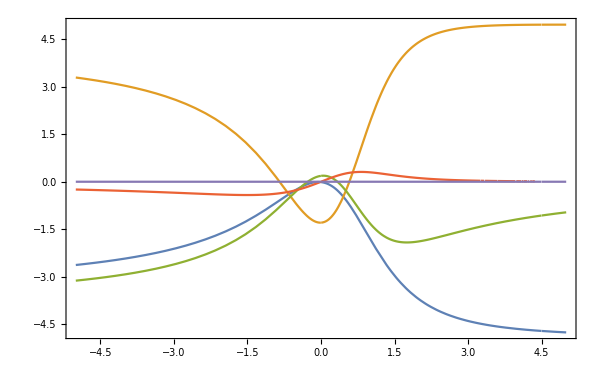

```mathematica
Plot[ coup, {Δ,-5,5},PlotLegends-> Placed[ MaTeX[#,Magnification->1]&/@{"J","K","\\Gamma","\\Gamma^{\\prime} "," D "},Scaled[{0.1,0.72}]  ]  ,  FrameLabel->{MaTeX["\\Delta/\\lambda \\quad (\\lambda=1)",Magnification->2] , MaTeX["\\text{Couplings}(\\Delta) \\quad eV_0=0",Magnification->1.75] } , Frame->True,  FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600(*,
 Epilog->{ Graphics[ Dashed, Opacity[.7],Line[ {{1/3,-4},{1/3,4}}] ]      } *)
]
```

```mathematica
figCouplings//InputForm
```

```mathematica
Directive[Opacity[1.], RGBColor[0.528488, 0.470624, 0.701351], AbsoluteThickness[1.6]]
```

Directive[Opacity[1.],RGBColor[0.528488, 0.470624, 0.701351],AbsoluteThickness[1.6]]

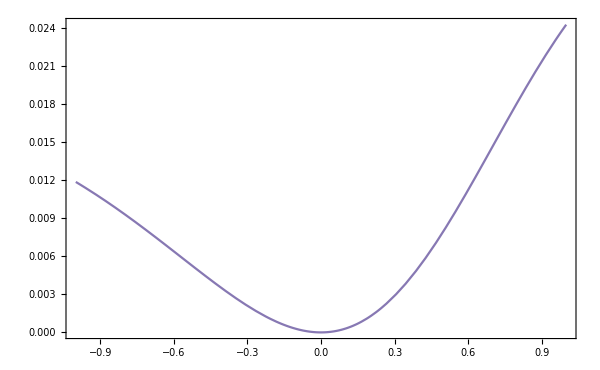

```mathematica
Plot[ coup[[5]], {Δ,-1,1},PlotStyle->Directive[Opacity[1.],RGBColor[0.528488,0.470624,0.701351],AbsoluteThickness[1.6]] 
,Frame->True,  FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,FrameLabel->{MaTeX["\\Delta/\\lambda",Magnification->2] , MaTeX["D(\\Delta)",Magnification->1] }   ]
```

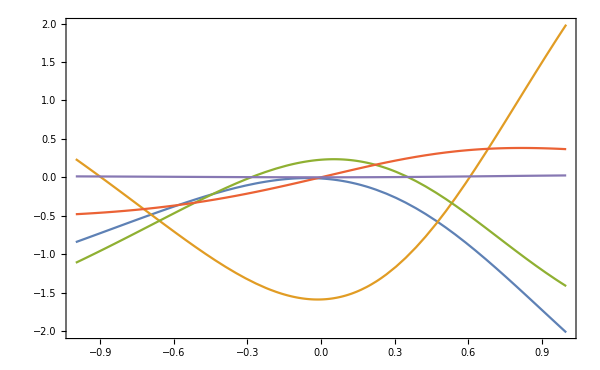

```mathematica
figCouplings
```

```mathematica
figCouplings=Plot[ coup , {Δ,-1,1},PlotLegends-> Placed[ MaTeX[#,Magnification->1]&/@{"J","K","\\Gamma","\\Gamma^{\\prime} "," D "},Scaled[{0.1,0.8}]  ],PlotLabel->MaTeX["eV_0=.3(U-3J_H)",Magnification->1.6]  ,  PlotStyle->Automatic,FrameLabel->{MaTeX["\\Delta/\\lambda \\quad (\\lambda=1)",Magnification->2] , MaTeX["\\text{Couplings}(\\Delta)",Magnification->1.75] } , Frame->True,  FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,
 Epilog->Inset[ 
Plot[ coup[[5]], {Δ,-1,1},PlotStyle->Directive[Opacity[1.],RGBColor[0.528488,0.470624,0.701351],AbsoluteThickness[1.6]] 
,Frame->True,  FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,10],ImageSize->600,FrameLabel->{MaTeX["\\Delta/\\lambda",Magnification->1] , MaTeX["D(\\Delta)",Magnification->1] } ]  ,   Scaled[{.5,.72}],{0,0},Scaled[0.4] ] 
]
```

-Graphics-

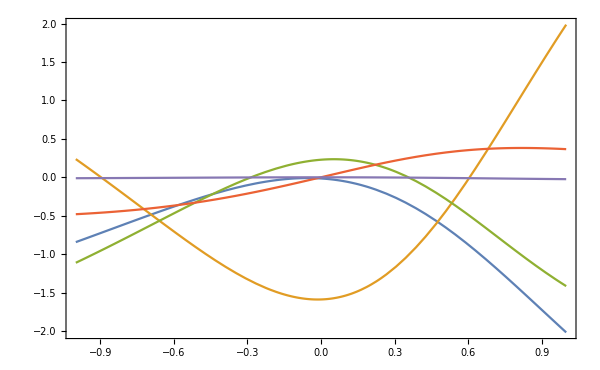

```mathematica
figCouplings=Plot[ coup , {Δ,-1,1},PlotLegends-> Placed[ MaTeX[#,Magnification->1]&/@{"J","K","\\Gamma","\\Gamma^{\\prime} "," D "},Scaled[{0.1,0.8}]  ],PlotLabel->MaTeX["eV_0=-.3(U-3J_H)",Magnification->1.6]  ,  PlotStyle->Automatic,FrameLabel->{MaTeX["\\Delta/\\lambda \\quad (\\lambda=1)",Magnification->2] , MaTeX["\\text{Couplings}(\\Delta)",Magnification->1.75] } , Frame->True,  FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,
 Epilog->Inset[ 
Plot[ coup[[5]], {Δ,-5,5},PlotStyle->Directive[Opacity[1.],RGBColor[0.528488,0.470624,0.701351],AbsoluteThickness[1.6]] 
,Frame->True,  FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,10],ImageSize->600,FrameLabel->{MaTeX["\\Delta/\\lambda",Magnification->1] , MaTeX["D(\\Delta)",Magnification->1] } ]  ,   Scaled[{.5,.7}],{0,-.031},Scaled[0.4] ] 
]
```

```mathematica
Print[ "Δ λ=",Δ λ,"; {J,K,Γ,Γp,DM}=", {J,K,Γ,Γp,DM} ,"; {J,K,Γ,Γp,DM}=",1/Abs[K]{J,K,Γ,Γp,DM}    ];
```

#### Loop for DM over K

```mathematica
Kc[eV0_,JH_,U_,t_]:=(2JH)/9( (t[[1]]-t[[3]])^2-3 t[[2]]^2 ) (eV0^2+3 JH^2-4 JH U+U^2)/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
tV={2};
ts = Table[ {5x,160,-12x,0,-60},{x,tV}]
U=2600;JH=300;
eVs=Table[(U-3JH)ξ,{ξ,0,.9,.1}]
```

{{10,160,-24,0,-60}}

{0.,170.,340.,510.,680.,850.,1020.,1190.,1360.,1530.}

```mathematica
DMeV0={};
Do[Module[{t1,t2,t3,t4,n,Ln,Δ,eV0,jm,J,K,Γ,Γp,DM,Hso,λ=150},ClearAll[v,V];
eV0=eVs[[ev]];
{t1,t2,t3,t4}=ts[[1]][[1;;4]];
n={1,1,1}/√3;
Ln=Sum[Subscript[L, a] n[[a]],{a,1,3}];
Δ=  1/3  eV0/(U-3JH) 1/λ;  
Hso=Sum[ Subscript[L, a].Subscript[S, a],{a,1,3}]+Δ Ln.Ln;
Subscript[v, 1]= (*-I*) Sort[Eigensystem[N[Hso]]][[2,2]]/Norm[Sort[Eigensystem[N[Hso]]][[2,2]]]//Chop;
Subscript[v, 2]= Sort[Eigensystem[N[Hso]]][[2,1]]/Norm[Sort[Eigensystem[N[Hso]]][[2,1]]]//Chop;
(*Subscript[v, 1]=N@{(-3 (3+√(9+4 (-1+Δ) Δ))+2 ⅈ Δ ((1+ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/(9+(2-4 ⅈ) Δ+3 √(9+4 (-1+Δ) Δ)),(-9+(3-6 ⅈ) √(9+4 (-1+Δ) Δ)-2 Δ (-2+2 Δ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),-(2 Δ ((1+2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),((4+4 ⅈ) Δ)/(9+(2-4 ⅈ) Δ+3 √(9+4 (-1+Δ) Δ)),0,1};
Subscript[v, 2]=N@{(2 Δ ((1+2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),(2 Δ ((1-2 ⅈ)+2 Δ+√(9+4 (-1+Δ) Δ)))/((4+2 ⅈ) Δ+3 ⅈ (3+√(9+4 (-1+Δ) Δ))),(9-(3-6 ⅈ) √(9+4 (-1+Δ) Δ)+2 Δ (-2+2 Δ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),((2-2 ⅈ) Δ+(3+3 ⅈ) (3 ⅈ+√(9+4 (-1+Δ) Δ)))/(-18+(4+8 ⅈ) Δ),1,0};
Subscript[v, 1]=Subscript[v, 1]/Norm[Subscript[v, 1]];
Subscript[v, 2]=Subscript[v, 2]/Norm[Subscript[v, 2]];*)
Table[Chop[Conjugate[Subscript[v, i]].Subscript[v, j]],{i,1,2},{j,1,2}];
V[m_,n_]:=Flatten[KroneckerProduct[Subscript[v, m],Subscript[v, n]]];

Tz=({{t1, t2, t4}, {t2, t1, t4}, {t4, t4, t3}});
T12=Tz;
HV0z=-ArrayFlatten[Table[Sum[(T12[[Alpha[sip],Alpha[s2]]]T12[[Alpha[s3],Alpha[si]]])/(Subscript[ΔE, L]-eV0)KroneckerDelta[Sigma[sip],Sigma[s2]]KroneckerDelta[Sigma[s3],Sigma[si]]Subscript[F, L][sjp,s2,s3,sj]+(T12[[Alpha[sjp],Alpha[s2]]]T12[[Alpha[s3],Alpha[sj]]])/(Subscript[ΔE, L]+eV0)KroneckerDelta[Sigma[sjp],Sigma[s2]]KroneckerDelta[Sigma[s3],Sigma[sj]]Subscript[F, L][sip,s2,s3,si],{s2,1,6},{s3,1,6},{L,0,2}],{sip,1,6},{si,1,6},{sjp,1,6},{sj,1,6}]];
PHV0z=ArrayFlatten[Table[Conjugate[V[i,j]].HV0z.V[k,l],{i,1,2},{k,1,2},{j,1,2},{l,1,2}]];PHV0z//MatrixForm;
JJ[i_,j_]:=Chop[Simplify[1/4 Tr[KroneckerProduct[Subscript[σ, i],Subscript[σ, j]].PHV0z]]];
jm=Table[JJ[i,j],{i,1,3},{j,1,3}];
Γp=(jm[[1,3]]+jm[[2,3]]+jm[[3,1]]+jm[[3,2]])/4; 
K=( jm[[3,3]]-(jm[[2,2]] +jm[[1,1]] )/2); J=(jm[[3,3]]-K);DM=(jm[[1,2]]-jm[[2,1]])/2;Γ=(jm[[1,2]]+jm[[2,1]])/2;

         Print[ "Δ λ=",Δ λ,"; {J,K,Γ,Γp,DM}=", {J,K,Γ,Γp,DM} ,"; {J,K,Γ,Γp,DM}=",1/Abs[K]{J,K,Γ,Γp,DM}    ];

AppendTo[ DMeV0, {eV0,DM/Abs[K]  }];


],{ev,1, Length@eVs}]
```

Δ λ=0.; {J,K,Γ,Γp,DM}={-0.0122577,-1.28975,0.185507,0,0.}; {J,K,Γ,Γp,DM}={-0.00950395,-1.,0.143832,0.,0.}

Δ λ=0.0333333; {J,K,Γ,Γp,DM}={-0.023315,-1.28743,-0.188327,0.0714336,-1.07563×10^-6}; {J,K,Γ,Γp,DM}={-0.0181097,-1.,-0.146282,0.0554853,-8.35483×10^-7}

Δ λ=0.0666667; {J,K,Γ,Γp,DM}={-0.0135757,-1.41407,-0.203494,0.00145537,-8.50065×10^-8}; {J,K,Γ,Γp,DM}={-0.00960046,-1.,-0.143907,0.00102921,-6.01149×10^-8}

Δ λ=0.1; {J,K,Γ,Γp,DM}={-0.0153731,-1.58968,-0.22881,0.0015982,-2.01833×10^-7}; {J,K,Γ,Γp,DM}={-0.00967056,-1.,-0.143934,0.00100536,-1.26964×10^-7}

Δ λ=0.133333; {J,K,Γ,Γp,DM}={-0.0184699,-1.88097,-0.270844,0.00873405,1.88067×10^-6}; {J,K,Γ,Γp,DM}={-0.00981937,-1.,-0.143991,0.00464337,9.99841×10^-7}

Δ λ=0.166667; {J,K,Γ,Γp,DM}={-0.0232656,-2.35939,-0.33979,0.00587502,1.87213×10^-6}; {J,K,Γ,Γp,DM}={-0.00986085,-1.,-0.144016,0.00249006,7.93479×10^-7}

Δ λ=0.2; {J,K,Γ,Γp,DM}={-0.0315437,-3.1758,-0.4575,0.00614454,-2.63036×10^-6}; {J,K,Γ,Γp,DM}={-0.00993254,-1.,-0.144058,0.0019348,-8.28253×10^-7}

Δ λ=0.233333; {J,K,Γ,Γp,DM}={-0.0653582,-4.64886,-0.674641,-0.173894,0.0000943955}; {J,K,Γ,Γp,DM}={-0.014059,-1.,-0.14512,-0.0374057,0.0000203051}

Δ λ=0.266667; {J,K,Γ,Γp,DM}={-0.082867,-8.11087,-1.16911,-0.0471057,0.0000307262}; {J,K,Γ,Γp,DM}={-0.0102168,-1.,-0.144141,-0.00580772,3.78827×10^-6}

Δ λ=0.3; {J,K,Γ,Γp,DM}={-0.198209,-19.4635,-2.80061,-0.0128758,8.66258×10^-6}; {J,K,Γ,Γp,DM}={-0.0101836,-1.,-0.14389,-0.000661533,4.45067×10^-7}

```mathematica
DMeV0
```

{{0.,0.},{170.,4.99219×10^-6},{340.,2.52789×10^-6},{510.,1.73114×10^-6},{680.,1.35174×10^-6},{850.,1.14245×10^-6},{1020.,1.02294×10^-6},{1190.,9.61623×10^-7},{1360.,9.47281×10^-7},{1530.,9.82175×10^-7}}